```mathematica
Clear["Global`*"];
```

## PHYSICAL CONSTANTS AND SYSTEM PARAMETERS

```mathematica
G=6.6743*10^-11;
c=299792.458*10^3;(*c in m/s*)hplanck=0.6770;
H0pl=3.23*hplanck*10^-18;
ρcritpl=(3*H0pl^2)/(8*Pi*G);

Rch=1.3710*10^26;
Λminus=((8*Pi*G*ρcritpl)/c^2)*(1/1.001);
Λplus=(8*Pi*G*ρcritpl)/c^2;
Λavg=(Λminus+Λplus)/2;
mminus=10^10*(1.988416*10^30);
mplus=1.001*mminus;
Rst=Power[(3*G*mminus)/(Λavg*c^2),1/3];
λ=1;
w0=-0.66;
(*This is the parameter R0,the valley is near here*)
RsolParameter=7.586121094208997*10^21;
σsol=4.909868011963678*10^-8;
```

## DEFINE POTENTIAL Veff(R)

```mathematica
Veff[R_]:=c^2/4*(2-(2 G mminus)/(c^2 R)-(2 G mplus)/(c^2 R)-(R^2 Λminus)/3-(R^2 Λplus)/3-((1+λ)^2 (6 G (mminus-mplus)+c^2 R^3 (Λminus-Λplus))^2)/(288 G^2 π^2 (RsolParameter^2 (RsolParameter/R)^(2 λ) (1+w0)+R^2 (-w0+λ))^2 σsol^2)-(8 G^2 π^2 R^2 (-w0+(RsolParameter/R)^(2 (1+λ)) (1+w0)+λ)^2 σsol^2)/(c^4 (1+λ)^2));
```

## FIND TRUE MINIMUM & CRITICAL EPSILON

```mathematica
solMin=FindMinimum[Veff[R],{R,RsolParameter}];
Rmin=R/. solMin[[2]];
Vmin=solMin[[1]];

(*Find the top of the barrier (Unstable Hill)*)
(*We search slightly to the right of the minimum*)
solHill=FindMaximum[Veff[R],{R,Rmin*1.01}];
Rhill=R/. solHill[[2]];
Vhill=solHill[[1]];

(*Calculate Critical Epsilon to cross the barrier*)
epsilonCrit=Sqrt[Vhill-Vmin];

Print["True Equilibrium Rmin: ",NumberForm[Rmin,10]];
Print["Hill Top Rhill:        ",NumberForm[Rhill,10]];
Print["Critical Epsilon:      ",epsilonCrit," m/s"];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

True Equilibrium Rmin: 7.586121094×10^21

Hill Top Rhill:        7.67728035×10^21

Critical Epsilon:      291715. m/s

## SOLVE DYNAMICS (Two Cases) Eq:R’’[t]==-V’[R[t]]

```mathematica
(*---CASE 1:STABLE (Small Kick)---*)
epsilon1=100;vKick1=Sqrt[2]*epsilon1;
ic1={R[0]==Rmin,R'[0]==vKick1};
period="7.949810162"×10^("14");
tMax=4*period;(*Time for a few oscillations*)solStable=NDSolve[{R''[tau]==-Veff'[R[tau]],ic1},R,{tau,0,tMax},Method->"StiffnessSwitching",MaxSteps->1000000];


(*---CASE 2:UNBOUNDED (Large Kick>Critical)---*)
epsilon2=292715;vKick2=Sqrt[2]*epsilon2;
ic2={R[0]==Rmin,R'[0]==vKick2};

solEscape=NDSolve[{R''[tau]==-Veff'[R[tau]],ic2,WhenEvent[R[tau]>=Rch,"StopIntegration"]},R,{tau,0,10^25},(*We give it a huge max time,WhenEvent will stop it early*)Method->"StiffnessSwitching",MaxSteps->1000000];

(*Extract the exact time it hit the horizon to use for the plot bounds*)
tEscape=(R["Domain"]/. solEscape[[1]])[[1,2]];
Print["Time to reach Cosmic Horizon: ",tEscape," seconds"];
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between tau = 1.65841×10^15 and tau = 1.70287×10^15.

Time to reach Cosmic Horizon: 1.6914×10^15 seconds

## PLOTTING

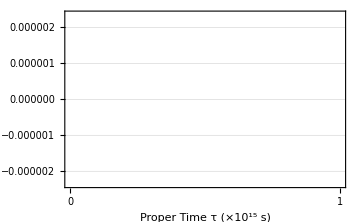

```mathematica
(*Custom Ticks for Plot 1:dividing values by 10^15 for display*)
timeTicks1=Table[{i,i/10^15},{i,0,tMax,1*10^15}];

(*Plot 1:Stable Oscillation Normalized to (R-R0)/R0*)
p1=Plot[((R[tau]/. solStable)-Rmin)/Rmin,{tau,0,tMax},Frame->True,PlotStyle->{Blue,Thickness[0.005]},GridLines->Automatic,ImageSize->Medium,FrameLabel->{Style["Proper Time τ (×\!\(\*SuperscriptBox[\(10\), \(15\)]\) s)",14,Bold,FontFamily->"Times"],Style["(R(τ) - \!\(\*SubscriptBox[\(R\), \(0\)]\)) / \!\(\*SubscriptBox[\(R\), \(0\)]\)",14,Bold,FontFamily->"Times"]},FrameTicks->{{Automatic,Automatic},{timeTicks1,Automatic}},FrameTicksStyle->Directive[FontSize->12,FontFamily->"Times"],LabelStyle->Directive[Black,FontFamily->"Times"],PlotLabel->None];

(*Plot 2:Unbounded Escape Normalized to R/Rch,running exactly to tEscape*)
p2=Plot[(R[tau]/. solEscape)/Rch,{tau,0,tEscape},Frame->True,PlotStyle->{Red,Thickness[0.005]},GridLines->Automatic,ImageSize->Medium,PlotRange->All,FrameLabel->{Style["Proper Time τ (s)",14,Bold,FontFamily->"Times"],Style["R(τ) / \!\(\*SubscriptBox[\(R\), \(ch\)]\)",14,Bold,FontFamily->"Times"]},FrameTicks->Automatic,(*Let Mathematica format the huge time numbers naturally*)FrameTicksStyle->Directive[FontSize->12,FontFamily->"Times"],LabelStyle->Directive[Black,FontFamily->"Times"],PlotLabel->None];

(*Show Side by Side*)
GraphicsGrid[{{p1,p2}},Spacings->{20,0},ImageSize->800]
```